# Arnoldi Iteration (Cont)

How and why does the Arnoldi eigenvalue work? We have a lot of slightly fancy machinery.  We construct and are looking in the Krylov space
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b}).
By definition any x∈𝒦_n(A,b)  satisfies x=c_0 b+c_1 A.b+ c_2 A^2.b+…+c_(n-1)A^(n-1).b=q(A).b where q(A) is the polynomial
	q(A)=c_0 Id+c_1 A+ c_2 A^2+…+c_(n-1)A^(n-1).
The question is what do we gain by writing/thinking of this as in terms of matrix polynomials!

We will see that the polynomial implicitly built by Arnoldi and other Krylov methods is the best polynomial in a very specific sense which gives convergence information.

## Polynomial Lemniscate: https://en.wikipedia.org/wiki/Polynomial_lemniscate

A lemniscate of a polynomial p(z) is a level set of |p(z)|=c.  You can plot these. They can be complicated.

```mathematica
p[z_]:=8.9-4 z-3 z^2+6 z^3-7 z^4+2 z^6+9 z^7+6 z^8-2 z^9
ContourPlot[ Abs[p[x+ I y]], {x, -1.5,1},{y,-1.2,1.2},
ContourLabels->All,
PlotPoints->100,
Epilog->{Red, Point[ReIm[NSolveValues[p[z]==0,z]]]},
Contours->{1,2,3,4,5,6,7,8,9,10}]
```

-Graphics-

You can see the zeros sitting in the middle of each blob.  Once the contours are small enough the blobs separate. Eventually if the roots are isolated each root is in one blob!

## Arnoldi Reminder

Just as a reminder: The Arnoldi process iteratively computes a nested sequence of orthogonal matrices Q_n∈ℝ^(m×n) and rectangular Upper Hessenberg matrices H_n∈ℝ^((n+1)×n).  Columns of Q_n are an orthonormal basis for the Krylov space	
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b}).
By construction, A maps 𝒦_n(A,b)→𝒦_(n+1)(A,b) with H_n the matrix for this map in the orthogonal basis. In other words, since H_n is Upper Hessenberg
	A.Q_n=Q_(n+1).H_n=Q_n.H_n[1:n,1:n]+H_n[n+1,n] q_(n+1). 
If the bottom corner of H_n is zero the Q_n is an invariant space of A and eigenvalues of the square Upper Hessenberg matrix
	(Ĥ)_n=H_n[1:n,1:n]
are eigenvalues of A.  Hopefully when H_n[n+1,n] is small the eigenvalues of (Ĥ)_n are close to eigenvalues of A.

```mathematica
Arnoldi[A_][{Q_,H_}]:= Module[{m,n,HNew,w,h,q},
{m,n}=Dimensions[Q];
HNew=ConstantArray[0,{n+1,n}];HNew⟦1;;n,1;;n-1⟧=H;
w=A.Q⟦All,n⟧;
Do[
q=Q⟦All,k⟧;
HNew⟦k,n⟧=q.w;
w=w-HNew⟦k,n⟧ q,
{k,1,n}];
HNew⟦n+1,n⟧=Norm[w];
w=w/HNew⟦n+1,n⟧;
{ArrayFlatten[({{Q, {w}ᵀ}})],HNew}
]
```

Remember:

Eigenvalues of (Ĥ)_n are the n roots of the characteristic polynomial p_n(z)=det(z I - (Ĥ)_n).

The eigenvalues λ_1,…,λ_n of (Ĥ)_n (called Ritz values or Arnoldi Approximations) approximate eigenvalues of A.

The matching eigenvector approximations v_i=Q_n.𝓋_i for i in (where (Ĥ)_n.𝓋_i=λ_i 𝓋_i) are called Ritz vectors.

## Arnoldi Lemniscate

The Arnoldi lemniscate is simply
	det(z I - (Ĥ)_n)=p_n(z)=||p_n(A).b||/||b||.
 As n gets bigger two things happen: the degree of the polynomial increases and hopefully the right hand side gets smaller.  Eventually (if we wait until n=m) the right hand side goes to zero and leaves the characteristic polynomial for the m eigenvalues of A.

Arnoldi detects “large” eigenvalues first.  Here is a test matrix with three “designed” large eigenvalues!

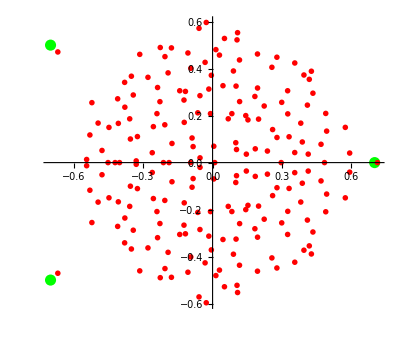

```mathematica
m=200;
A=RandomReal[{-1/√m,1/√m},{m,m}]; 
{i,j,k}={12,17,18};{γ,α,β}={0.7,-0.7,0.5};
AExtra = ({{γ, 0, 0}, {0, α, β}, {0, -β, α}});A⟦{i,j,k},{i,j,k}⟧=AExtra;
EValPic=ListPlot[{ReIm[Eigenvalues[AExtra]],ReIm[Eigenvalues[A]]},
PlotRange->All,
PlotStyle->{{Green, PointSize[0.02]},{Red,PointSize[0.01]}},
AspectRatio->Automatic]
```

Lets see what the Arnoldi lemniscate pictures look like for this.

```mathematica
Clear[MaxIter,Q0,H0,HData,p,c,n,z]
MaxIter=20;
b=Normalize[RandomReal[{-1,1},m]];
{Q0,H0}={{b}ᵀ,{{}}};
HData=NestList[Arnoldi[A],{Q0,H0},MaxIter]⟦2;;MaxIter,2⟧;
TabView[Map[MatrixPlot,HData],MaxIter-1];
Clear[p,n]
TabView[
Table[
H=HData⟦n⟧;
p[n][z_]=CharacteristicPolynomial[H⟦1;;n⟧,z];
c[n]=Norm[p[n][A].b];
{p[n][z],c[n],H⟦-1,-1⟧},
{n,1, Length[HData]}],Length[HData]];
TabView[
Table[ 
Show[EValPic,
ContourPlot[Abs[p[n][x+I y]]==c[n],{x,-1,1},{y,-0.7,0.7},
PlotPoints->200],
Epilog->Point[ReIm[Eigenvalues[HData⟦n,1;;n⟧]]]],
{n, 1, Length[HData]}]
]
```

12345678910111213141516171819

You can see the blue curve bulge, then pinch of, and then shrink down on the “external” eigenvalues.  This is what Arnoldi does.  The question is can we use polynomials to understand the asymptotic convergence.

## Arnoldi is “Optimal”

The Arnoldi process produces the best monic (lead coefficient equals one) polynomial in the sense that 
	p_n(z)=det(z I-(Ĥ)_n)=argmin_(p∈𝒫_n)||p(A).b||
 where 𝒫_n={z^n+c_(n-1)z^(n-1)+…+c_2 z^2+c_1 z+c_0}.  This looks very weird but it is really just the orthogonality in the Arnoldi process.

Why:
For any p∈𝒫_n we have p(A).b=A^n.b-Q_n.y for some y∈ℂ^n and so
	argmin_(p∈𝒫_n)||p(A).b|| | ⟺ | y_best=argmin_(y∈ℂ^n)||A^n.b-Q_n.y||.
The point in 𝒦_n(A,b) nearest A^n.b is simply y_best=(Q_n)†.A^n.b.  If we continued the Arnoldi process we would get the Hessenberg decomposition 
	A=Q_m.(Ĥ)_m.(Q_m)†
of A

```mathematica
HData⟦3⟧
```

{{0.0349624,-0.0235984,0.0287475},{0.582569,0.0228445,-0.00169296},{0,0.612454,-0.0175021},{0,0,0.584857}}

-Graphics-

(0.0380051 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0231506 | 0.0194579 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00651617 | -0.0474367 | 0.0266952 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.00512716 | 0.0033631 | -0.138676 | 0.0768199 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0106174 | 0.0110792 | -0.0554472 | -0.150987 | -0.0707177 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.00663382 | 0.00500878 | 0.0446119 | -0.0156434 | -0.212983 | 0.191716 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.00341978 | 0.00719899 | 0.00524357 | 0.0741492 | 0.0846385 | -0.285321 | -0.206959 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.001059 | -0.00277393 | -0.0050757 | -0.00988643 | 0.120972 | -0.192454 | -0.365524 | 0.248017 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000228363 | -0.00289858 | -0.00219778 | -0.00238455 | 0.0225936 | 0.143776 | 0.240409 | -0.404729 | -0.262406 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000362892 | -0.0000281714 | -0.00277443 | 0.00168653 | -0.00101372 | -0.0310955 | 0.160183 | -0.253036 | -0.414248 | 0.245395 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000176892 | 0.000950516 | 0.000713869 | -0.00322729 | 0.00111137 | -0.00559773 | 0.0404457 | 0.148295 | 0.287928 | -0.369362 | -0.310024 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.000478834 | 0.000709015 | 0.000669591 | -0.0000259017 | -0.00208918 | -0.00550916 | -0.00671743 | -0.0570367 | 0.177157 | -0.264339 | -0.402538 | 0.22795 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0000649868 | -0.000792294 | -0.000486671 | 0.00111374 | 0.000684258 | -0.00620618 | 0.000740542 | 0.000264345 | 0.0502563 | 0.174947 | 0.283007 | -0.435072 | -0.218843 | 1 | 0 | 0 | 0 | 0 | 0 | 0
-0.000064237 | 0.0000508671 | -0.000840891 | 0.000284198 | 0.000712131 | -0.0000646179 | -0.00756294 | 0.000919551 | -0.000149731 | -0.070031 | 0.206942 | -0.222702 | -0.456284 | 0.122546 | 1 | 0 | 0 | 0 | 0 | 0
0.0000153403 | -0.0000323065 | -5.5581×10^-6 | -0.000768424 | -0.000507856 | 0.000920329 | -0.000229524 | -0.00672294 | -0.00670401 | -0.00301352 | 0.0669114 | 0.204089 | 0.238234 | -0.487037 | -0.126958 | 1 | 0 | 0 | 0 | 0
-6.34729×10^-6 | -0.0000153858 | -0.000137324 | -0.000158422 | -0.000533707 | 0.00104214 | -0.000529982 | 0.00124321 | -0.00806399 | 0.00758351 | -0.00255245 | -0.0813828 | 0.218113 | -0.187677 | -0.484747 | 0.0620282 | 1 | 0 | 0 | 0
-0.0000104364 | -7.03776×10^-6 | 0.0000179942 | -0.000123999 | 0.00016619 | -0.000701521 | -0.00181335 | 0.000284744 | 0.000316285 | -0.0110752 | -0.0138438 | -0.00803398 | 0.067491 | 0.210878 | 0.213658 | -0.506592 | -0.115026 | 1 | 0 | 0
-2.83298×10^-6 | 7.68964×10^-6 | -0.0000328781 | -0.0000178531 | -0.00010286 | -0.00016783 | -0.000600216 | 0.00198103 | 0.000370561 | 0.00134645 | -0.0106364 | 0.00736837 | -0.00487285 | -0.0672381 | 0.194832 | -0.220853 | -0.475162 | 0.128619 | 1 | 0
8.04812×10^-7 | 1.45421×10^-6 | -7.63278×10^-6 | -0.0000347062 | 0.0000272141 | -0.0000593809 | 0.000353047 | -0.000592321 | -0.0021463 | 0.000310335 | -0.00434991 | -0.0127924 | -0.00655261 | -0.00155187 | 0.069285 | 0.194714 | 0.205339 | -0.482262 | -0.0989478 | 1)

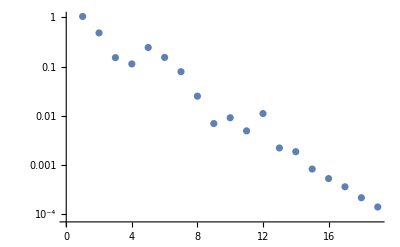

```mathematica
MatrixPlot[
Table[
CoefficientList[p[n][(-1)^n z],z,MaxIter],
{n, MaxIter-1}],
PlotLegends->Automatic]
MatrixForm[
Table[
CoefficientList[p[n][(-1)^n z],z,MaxIter],
{n, MaxIter-1}]]
ListLogPlot[Table[c[n],{n,1,MaxIter}]]
```

```mathematica
Table[
CoefficientList[p[7][-z]
p[6][z]
```

-0.000687826+0.0138322 z+0.0247633 z^2+0.0159576 z^3+0.0971679 z^4-0.0559848 z^5-0.275902 z^6+z^7

0.00790182-0.0143513 z+0.0147749 z^2-0.0676133 z^3-0.0277153 z^4+0.146924 z^5+z^6

```mathematica
?CharacteristicPolynomial
```

The book says that

Old Stuff

## Arnoldi Eigenvalues

The Arnoldi iteration can continue as long as w≠0 after projecting out all the previous directions. If w=0 then Q describes an invariant space for A and A.Q=Q.ℋ where ℋ is simply the square Upper Hessenberg upper block of H.  If this happens the eigenvalues of ℋ are eigenvalues of A. The bottom element of H does not need to be zero for the eigenvalues of ℋ (called Ritz values or Arnoldi estimates) to be useful approximations to large eigenvalues of A.

If we look at the Ritz values we can see them converge. In this case a cartoon is worth a lot of words.

```mathematica
m=123;
A=RandomReal[{-1,1},{m,m}];
EvalPic=ListPlot[ReIm[Eigenvalues[A]],
PlotRange->All,PlotStyle->{Green,PointSize[0.02]},
AspectRatio->Automatic,
Frame->True];
MaxIter=m;
b=RandomReal[{-1,1},m];
{Q0,H0}={{Normalize[b]}ᵀ,{{}}};
HData=NestList[Arnoldi[A],{Q0,H0},MaxIter]⟦2;;-1,2,1;;-2⟧;
RitzValues=Map[Eigenvalues,HData];
TableForm[RitzValues];
k=23;
ListAnimate[Map[
Show[EvalPic,Epilog->{Red, PointSize[0.015],Point[ReIm[#]]}]&,RitzValues],
6]
```

This with appropriate refinements and flourishes is what almost all eigenvalue algorithms for sparse non-symmetric matrices do.